#### Preamble

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

```mathematica
SetDirectory[NotebookDirectory[]]
<<"MaTeX`"
<<"~/Documents/Wolfram/Wolfram_scripts/Nano_CSM_SDistAll.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Nano_CSM_Biosensor.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/GradientDescend.wls"
```

/home/juanathan/Documents/Collaborations/En progreso/2022-06-INAOE-CSM/2-Reflectance_Measurments_NormalDist

```mathematica
fs = 10;
texStyle={FontFamily->"Latin Modern Math",FontSize->fs,Black};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
colors = Flatten@Prepend[colors,{Red,Darker[Green]}]

graphsOptsExp= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[#]&/@colors)};
graphsOptsTeo= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[#]&/@colors)};
```

{RGBColor[1, 0, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

#### Sample Characteristics

```mathematica
film = Import[#,"Data"]& @@ FileNames["1*fill.csv"];
TableForm[film[[2;;]],TableHeadings->{None,film[[1]]}]
radius = film[[2;;,2]];
muSigma = film[[2;;,{2,3}]];
cfrac = film[[2;;,4]]/100;
```

Nominal Au Thickness [+-0.2 nm] | Mean radius [nm] |  | Fill factor [100%] | 
3 | 5.78 | 1.89 | 20.3 | 0.6
5 | 7.3 | 2.3 | 22.1 | 0.1

```mathematica
nMat  = Import[#,"Data"] & @@ FileNames["3*Ind.csv"];
nMat = Drop[nMat,1];
nM = nMat[[1,2]]
```

1.33278

## Experimental Spectra AuNI

```mathematica
(files = FileNames["*","Extinction*"])//TableForm
data = Import[#,"Data"]& /@ files;
wlen = Range[wlL = 450,wlR = 850,5.];
ang = {64.9,72.9} *Pi/180.;
nNP=JohnsonChristyAuRefSize[#1,#2]&;
pl = MapThread[Style["a = "<>ToString[#1]<>" nm, Θ = "<> ToString[#2],texStyle]&,{radius,cfrac}];
labels = Outer[#1<>" - θ_i = "<>#2<>"°"&,{"s-pol","p-pol"},ToString/@(ang*180/Pi)];
```

Extinction AuNI/Extinction AuNI nominal thickness d3nm_5nm 64_9deg.xlsx
Extinction AuNI/Extinction AuNI nominal thickness d3nm_5nm 72_9deg.xlsx

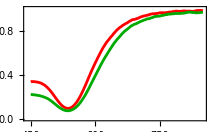
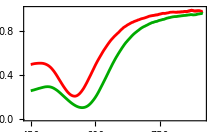
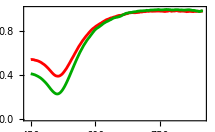
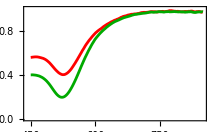

```mathematica
spectra = Map[Drop[#,4]&, data,{2}] (*Delete Headers*) ;
spectra = Map[Select[#,Function[list,wlL<=list[[1]]<= wlR]]&,spectra,{2}](*Choosing in the Visible*);
spectra = Map[Table[#[[{1,i}]]*{1,.01},{i,2,Length[#]}]&,spectra,{3}]
spectra = Transpose[spectra,{2,1,4,3,5}](*[[pol, ang, thickness, lda, Ext]]*);
spectra=spectra[[;;,;;,{1,2}]];

islandExt = Map[ListLinePlot[#,Evaluate[graphsOptsExp],PlotRange->{0,1}]&,spectra,{2}]
```

```mathematica
Map[SortBy[#,Last][[1]] &,spectra,{3}] //Grid
```

{{536.713,0.0930782},{536.066,0.0709467}} | {{552.366,0.204016},{569.534,0.0998457}}
{{513.499,0.386172},{511.68,0.224258}} | {{525.698,0.400039},{522.845,0.194133}}

## FitModel (Nominal) s Pol

{2,2,2,3138,2}

{450.121,453.394,456.665,459.934,463.203,466.47,469.736,473.,476.264,479.525,482.786,486.045,489.303,492.559,495.814,499.068,502.321,505.572,508.821,512.07,515.317,518.563,521.807,525.05,528.291,531.532,534.77,538.008,541.244,544.479,547.712,550.944,554.175,557.404,560.632,563.859,567.084,570.308,573.53,576.751,579.971,583.189,586.406,589.621,592.835,596.048,599.259,602.469,605.678,608.885,612.09,615.295,618.497,621.699,624.899,628.098,631.295,634.491,637.685,640.878,644.07,647.26,650.449,653.636,656.822,660.006,663.189,666.371,669.551,672.73,675.907,679.083,682.258,685.431,688.602,691.772,694.941,698.108,701.274,704.439,707.601,710.763,713.923,717.082,720.239,723.394,726.549,729.701,732.853,736.002,739.151,742.298,745.443,748.587,751.729,754.87,758.01,761.148,764.285,767.42,770.553,773.685,776.816,779.945,783.073,786.199,789.324,792.447,795.569,798.689,801.808,804.925,808.041,811.155,814.268,817.379,820.489,823.597,826.704,829.809,832.912,836.015,839.115,842.214,845.312,848.408}

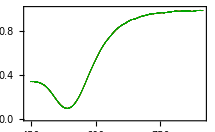
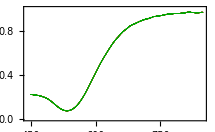
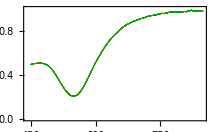
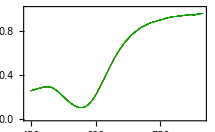

```mathematica
spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,3150,25];
lambda = wl[[take]]
pol = 1;

Map[ListPlot[{#[[;;,2]],#[[;;,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[pol]],{2}]
```

```mathematica
muSigma
cfrac
```

{{5.78,1.89},{7.3,2.3}}

{0.203,0.221}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
nomS = Array[(a = muSigma[[#2,1]];
            cf = cfrac[[#2]];
            sigma = muSigma[[#2,2]];
            f = norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
{2,2}];(*ang,case*)
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

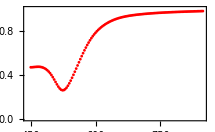
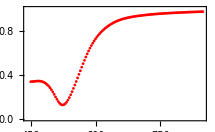
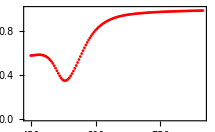
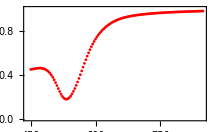

{{{525.05,0.258117},{525.05,0.123729}},{{531.532,0.344485},{534.77,0.176383}}}

```mathematica
Map[ ListPlot[#,DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&, nomS, {2}]

algo = Map[Transpose[{lambda,#}]&,nomS,{2}];
Map[SortBy[#,Last][[1]] &,algo,{2}]
```

## FitModel (Nominal) p Pol

{2,2,2,3138,2}

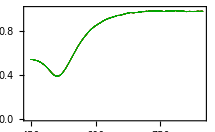
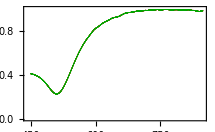
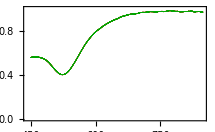
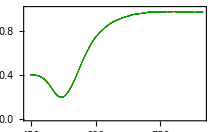

```mathematica
spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,3150,25];
lambda = wl[[take]];
pol = 2;

Map[ListPlot[{#[[;;,2]],#[[;;,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[pol]],{2}]
```

```mathematica
muSigma
cfrac
```

{{5.78,1.89},{7.3,2.3}}

{0.203,0.221}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
nomP = Array[(a = muSigma[[#2,1]];
            cf = cfrac[[#2]];
            sigma = muSigma[[#2,2]];
            f = norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
{2,2}];(*ang,case*)
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

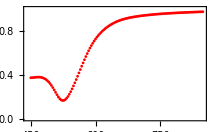
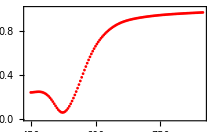
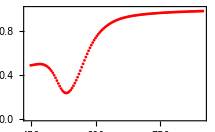
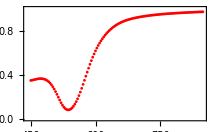

{525.05,0.164818} | {525.05,0.0552833}
{534.77,0.232749} | {538.008,0.0789588}

{{{525.05,0.164818},{525.05,0.0552833}},{{534.77,0.232749},{538.008,0.0789588}}}

```mathematica
Map[ ListPlot[#,DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&, nomP, {2}]

algo = Map[Transpose[{lambda,#}]&,nomP,{2}];
Map[SortBy[#,Last][[1]] &,algo,{2}] //Grid
Map[SortBy[#,Last][[1]] &,algo,{2}]
```

## FitModel (Gradient Descend) s Pol

```mathematica
spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,3150,25];
lambda = wl[[take]];
pol = 1;

Map[ListPlot[{#[[;;,2]],#[[;;,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[pol]],{2}]
```

{2,2,2,3138,2}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
radiusS = {{3.56,5.29},{3.45,4.54}}
cfracS = {{0.25,0.27},{0.25,0.27}}
```

{{3.56,5.29},{3.45,4.54}}

{{0.25,0.27},{0.25,0.27}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
fitS = Array[(a = radiusS[[#1,#2]];
            cf = cfracS[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
{2,2}];(*ang,case*)
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

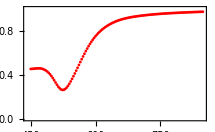
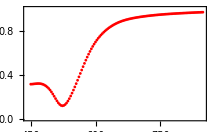
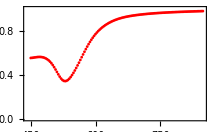
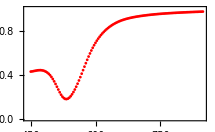

{525.05,0.260849} | {525.05,0.116514}
{531.532,0.341148} | {534.77,0.177656}

```mathematica
Map[ ListPlot[#,DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&, fitS, {2}]

algo = Map[Transpose[{lambda,#}]&,fitS,{2}];
Map[SortBy[#,Last][[1]] &,algo,{2}] //Grid
```

## FitModel (Gradient Descend) p Pol

```mathematica
spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,3150,25];
lambda = wl[[take]];
pol = 2;

Map[ListPlot[{#[[;;,2]],#[[;;,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[pol]],{2}]
```

{2,2,2,3138,2}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
radiusP = {{3.29,4.03},{3.34,4.11}}
cfracP = {{0.17, 0.19},{0.17, 0.19}}
```

{{3.29,4.03},{3.34,4.11}}

{{0.17,0.19},{0.17,0.19}}

```mathematica
indAu = Transpose[Table[{nM,1.5},{i,lambda}]];
fitP = Array[(a = radiusP[[#1,#2]];
            cf = cfracP[[#1,#2]];
            sigma = muSigma[[#2,2]];
            f = norm2[CSMBioReflectionInt[ang[[#1]],indAu,lambda,cf,{a,sigma},"SizeDistribution"->"Normal"][[pol]]])&,
{2,2}];(*ang,case*)
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

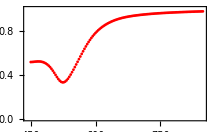
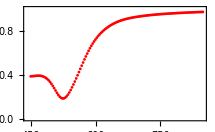
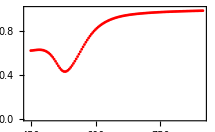
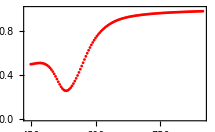

{525.05,0.330141} | {525.05,0.183295}
{531.532,0.427798} | {534.77,0.253295}

```mathematica
Map[ ListPlot[#,DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&, fitP, {2}]

algo = Map[Transpose[{lambda,#}]&,fitP,{2}];
Map[SortBy[#,Last][[1]] &,algo,{2}] //Grid
```

## Experimental Spectra AuNI

## Figs for the article (Nominal)

```mathematica
PlotGrid = ResourceFunction["PlotGrid"]
CombinePlots = ResourceFunction["CombinePlots"]
```

```mathematica
graphsOptsExp = {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 400, PlotStyle-> (Directive[#,Thick]&/@colors)};
graphsOptsS= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 400, PlotStyle-> (Directive[#,Dashed]&/@colors)};
graphsOptsP= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 400, PlotStyle-> (Directive[#,DotDashed]&/@colors)};
fs=12
texStyle={FontFamily->"Latin Modern Math",FontSize->fs,Black};
```

12

```mathematica
RGBcolors = {{255,0,0},{0,170,0}}
 RGBcolors = {RGBcolors,RGBcolors}
```

{{255,0,0},{0,170,0}}

{{{255,0,0},{0,170,0}},{{255,0,0},{0,170,0}}}

### Single labes

```mathematica
sampleD = {{3,5},{3,5}};
(***********
Legends foe each sample
************)
radiusExp = {5.78,7.3};
cfracExp = {0.20,0.22};
texLegendExp = Function[{str},
                MaTeX[#,FontSize->12, ContentPadding->True] &/@{
                    "\\mu = "<>ToString[NumberForm[str[[1]],{3,2}]]<>" \\text{ nm}", "\\Theta = "<>ToString[NumberForm[str[[2]],{3,2}]]
                  }];    
lines = LineLegend[{Directive[Black],Directive[Black,Dashed]},{Style["Experiment",texStyle],Style["Theory",texStyle]},LegendLayout->"Row",LegendMarkerSize->15];
explab = MapThread[texLegendExp[{#1,#2}]&,{radiusExp,cfracExp},1];
explab = Row[#,","]& /@ explab;
explab = SwatchLegend[{Red,Darker[Green]},explab, LegendLayout->"Row"];
explab = Row[Flatten[{lines, explab}]," ",Frame->True,RoundingRadius->6]
Export["Exp-vs-Model-Label-Nom.pdf",explab]
```

Exp-vs-Model-Label-Nom.pdf

```mathematica
final = {0,0};
polangles = Outer[MaTeX["\\begin{aligned} &"<>#1<>" \\text{ Pol.}\\\\ &"<>#2<>"\\end{aligned}",ContentPadding->False]&,{"s","p"},{"\\theta_i = 64.9^\\circ","\\theta_i = 72.9^\\circ"}]

pol = 1 (*s*); dummy = {0,0};
dummy[[1]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]] &, spectra[[pol]]];
dummy[[2]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsS]] &, nomS];

final[[1]] = MapThread[Show[{#1,#2},FrameLabel->{Style["Wavelength [nm]",texStyle], Style["Reflectivity"]},
                    AspectRatio->1/2.35]&,
                    dummy];

pol = 2 (*p*); dummy = {0,0};
dummy[[1]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]] &, spectra[[pol]]];
dummy[[2]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsS]] &, nomP];

final[[2]] = MapThread[Show[{#1,#2},FrameLabel->{Style["Wavelength [nm]",texStyle], Style["Reflectivity"]},
                    AspectRatio->1/2.35]&,
                    dummy];
                    
final = MapThread[
        Show[#1,ImageSize->Medium,Epilog->{Inset[#2,{790,.25}]}]&,
        {final, polangles},2];         
PlotGrid[final,ImageSize->685*3/5,Spacings->5, "ShowFrameLabels"->Automatic, "HideOuterTickLabels" -> Automatic]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

-Graphics-

```mathematica
Export["Exp-vs-Model-Spacing-Nom.svg",PlotGrid[final,ImageSize->685*3/5,Spacings->5, "ShowFrameLabels"->Automatic, "HideOuterTickLabels" -> Automatic]]
```

Exp-vs-Model-Spacing-Nom.pdf

## Figs for the article (Gradient Descend Fit)

```mathematica
PlotGrid = ResourceFunction["PlotGrid"]
CombinePlots = ResourceFunction["CombinePlots"]
```

```mathematica
colors[[2]] =Darker[Green];
graphsOptsExp = {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 400, PlotStyle-> (Directive[#,Thick]&/@colors)};
graphsOptsS= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 400, PlotStyle-> (Directive[#,Dashed]&/@colors)};
graphsOptsP= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 400, PlotStyle-> (Directive[#,DotDashed]&/@colors)};
fs=12
texStyle={FontFamily->"Latin Modern Math",FontSize->fs,Black};
```

12

```mathematica
MaTeX["\\color[RGB]{255,0,0} x",  "Preamble"->{"\\usepackage{color}"}]
 MaTeX["\\color[RGB]{0,170,0} x",  "Preamble"->{"\\usepackage{color}"}]
 
 RGBcolors = {{255,0,0},{0,170,0}}
 RGBcolors = {RGBcolors,RGBcolors}
```

-Graphics-

-Graphics-

{{255,0,0},{0,170,0}}

{{{255,0,0},{0,170,0}},{{255,0,0},{0,170,0}}}

### All labels

```mathematica
final = {0,0};
(***********
Legends foe each sample
************)
radiusExp = {{5.78,7.3},{5.78,7.3}};
cfracExp = {{0.20,0.22},{0.20,0.22}};

texLegend = Function[{str,col},
                MaTeX["\\color[RGB]"<>ToString[col]<> #,FontSize->12,  "Preamble"->{"\\usepackage{color}"},ContentPadding->False] &/@{
                    "a^\\text{exp} = "<>ToString[str[[1]]]<>" \\text{ nm}", "\\Theta^\\text{exp} = "<>ToString[str[[2]]], 
                    "a^\\text{teo} = "<>ToString[str[[3]]]<>" \\text{ nm}", "\\Theta^\\text{teo} = "<>ToString[str[[4]]]
                  }];

lines = LineLegend[{Directive[Black],Directive[Black,Dashed]},{Style["Exp",texStyle],Style["Fit",texStyle]},LegendLayout->"Row",LegendMarkerSize->15];                                            
legends = {MapThread[texLegend[{#1,#2,#3,#4},#5]&,{radiusExp,cfracExp,radiusS,cfracS, RGBcolors},2],
          MapThread[texLegend[{#1,#2,#3,#4},#5]&,{radiusExp,cfracExp,radiusP,cfracP, RGBcolors},2]} (*[[pol,ang,sample,text]]*)
legends = Map[Column,legends,{3}];
polangles = Outer[MaTeX["\\begin{aligned} &"<>#1<>" \\text{ Pol.}\\\\ &"<>#2<>"\\end{aligned}",ContentPadding->False]&,{"s","p"},{"\\theta_i = 64.9^\\circ","\\theta_i = 72.9^\\circ"}]
(***********
Each individual plot per polarization  and angle of incidence
************)
pol = 1 (*s*); dummy = {0,0};
dummy[[1]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]] &, spectra[[pol]]];
dummy[[2]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsS]] &, fitS];

final[[1]] = MapThread[Show[{#1,#2},FrameLabel->{Style["Wavelength [nm]",texStyle], Style["Reflectivity"]},
                    AspectRatio->1/2.75]&,
                    dummy];

pol = 2 (*p*); dummy = {0,0};
dummy[[1]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]] &, spectra[[pol]]];
dummy[[2]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsS]] &, fitP];

final[[2]] = MapThread[Show[{#1,#2},FrameLabel->{Style["Wavelength [nm]",texStyle], Style["Reflectivity"]},
                    AspectRatio->1/2.75]&,
                    dummy];
                    
final = MapThread[
        Show[#1,ImageSize->Medium,Epilog->{Inset[#2[[1]],{695,.3}],Inset[#2[[2]],{805,.3}],Inset[#3,{475,.85}],Inset[#4,{750,.65}]}]&,
        {final, legends, polangles,ConstantArray[lines,{2,2}]},2]
```

{{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
PlotGrid[final,ImageSize->685]
Export["Exp-vs-Model-All.svg",PlotGrid[final,ImageSize->700]]
```

-Graphics-

Exp-vs-Model-All.pdf

### Single labes

```mathematica
MaTeX[5]
```

-Graphics-

```mathematica
final = {0,0};
sampleD = {{3,5},{3,5}};
(***********
Legends foe each sample
************)
radiusExp = {5.78,7.3};
cfracExp = {0.20,0.22};
texLegendExp = Function[{str},
                MaTeX[#,FontSize->12, ContentPadding->True] &/@{
                    "\\mu = "<>ToString[NumberForm[str[[1]],{3,2}]]<>" \\text{ nm}", "\\Theta = "<>ToString[NumberForm[str[[2]],{3,2}]]
                  }];    
lines = LineLegend[{Directive[Black],Directive[Black,Dashed]},{Style["Experiment",texStyle],Style["Theory",texStyle]},LegendLayout->"Row",LegendMarkerSize->15]
explab = MapThread[texLegendExp[{#1,#2}]&,{radiusExp,cfracExp},1]
explab = Row[#,","]& /@ explab
explab = SwatchLegend[{Red,Darker[Green]},explab, LegendLayout->"Row"]
explab = Row[Flatten[{lines, explab}]," ",Frame->True,RoundingRadius->6]
Export["Exp-vs-Model-Label.svg",explab]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

{,,-Graphics--Graphics-,,,-Graphics--Graphics-}

Exp-vs-Model-Label.pdf

```mathematica
texLegendTeo = Function[{str,col},
                MaTeX["\\color[RGB]"<>ToString[col]<> #,FontSize->12,  "Preamble"->{"\\usepackage{color}"},ContentPadding->False] &/@{
                    "a^\\text{CSM}= "<>ToString[str[[1]]]<>" \\text{ nm}", "\\Theta^\\text{CSM} = "<>ToString[str[[2]]]
                  }];               
                                            
legends = {MapThread[texLegendTeo[{#1,#2},#3]&,{radiusS,cfracS, RGBcolors},2],
          MapThread[texLegendTeo[{#1,#2},#3]&,{radiusP,cfracP, RGBcolors},2]} (*[[pol,ang,sample,text]]*)
legends = Map[Transpose,legends,{2}];
legends = Map[Column[#,Spacings->1.2]&,legends,{3}];
polangles = Outer[MaTeX["\\begin{aligned} &"<>#1<>" \\text{ Pol.}\\\\ &"<>#2<>"\\end{aligned}",ContentPadding->False]&,{"s","p"},{"\\theta_i = 64.9^\\circ","\\theta_i = 72.9^\\circ"}];
(***********
Each individual plot per polarization  and angle of incidence
************)
pol = 1 (*s*); dummy = {0,0};
dummy[[1]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]] &, spectra[[pol]]];
dummy[[2]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsS]] &, fitS];

final[[1]] = MapThread[Show[{#1,#2},FrameLabel->{Style["Wavelength [nm]",texStyle], Style["Reflectivity"]},
                    AspectRatio->1/2.75]&,
                    dummy];

pol = 2 (*p*); dummy = {0,0};
dummy[[1]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]] &, spectra[[pol]]];
dummy[[2]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsS]] &, fitP];

final[[2]] = MapThread[Show[{#1,#2},FrameLabel->{Style["Wavelength [nm]",texStyle], Style["Reflectivity"]},
                    AspectRatio->1/2.75]&,
                    dummy];
                    
final = MapThread[
        Show[#1,ImageSize->Medium,Epilog->{Inset[#2[[1]],{695,.25}],Inset[#2[[2]],{805,.25}],Inset[#3,{475,.85}]}]&,
        {final, legends, polangles},2]
```

{{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
PlotGrid[final,ImageSize->685,Spacings->5, "ShowFrameLabels"->Automatic, "HideOuterTickLabels" -> Automatic]
```

-Graphics-

```mathematica
Export["Exp-vs-Model.svg",PlotGrid[final,ImageSize->700]]
Export["Exp-vs-Model-Spacing.svg",PlotGrid[final,ImageSize->685,Spacings->5, "ShowFrameLabels"->Automatic, "HideOuterTickLabels" -> Automatic]]
```

Exp-vs-Model.pdf

Exp-vs-Model-Spacing.pdf

## Figs for the article (Both)

```mathematica
PlotGrid = ResourceFunction["PlotGrid"]
CombinePlots = ResourceFunction["CombinePlots"]
```

```mathematica
colors[[2]] =Darker[Green];
fs=10
texStyle={FontFamily->"Latin Modern Math",FontSize->fs,Black};

graphsOptsExp = {Mesh-> All,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 400, 
                  PlotStyle-> Append[(Directive[#,Thick]&/@colors),PointSize[.005]]};
graphsOptsNom= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 400, PlotStyle-> (Directive[#]&/@colors)};
graphsOptsFit= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 400, PlotStyle-> (Directive[#,Dashed]&/@colors)};

RGBcolors = {{255,0,0},{0,170,0}}
```

10

{{255,0,0},{0,170,0}}

### Single labes

```mathematica
final = {0,0};
sampleD = {{3,5},{3,5}};
polangles = Outer[MaTeX["\\begin{aligned} &"<>#1<>" \\text{ pol.}\\\\ &"<>#2<>"\\end{aligned}",ContentPadding->False, FontSize->fs]&,{"s","p"},{"\\theta_i = 64.9^\\circ","\\theta_i = 72.9^\\circ"}]
(***********
Legends foe each sample
************)
radiusExp = {5.78,7.3};
cfracExp = {0.20,0.22};
texLegendExp = Function[{str},
                MaTeX[#,FontSize->11, ContentPadding->True] &/@{
                    "\\mu = "<>ToString[NumberForm[str[[1]],{3,2}]]<>" \\text{ nm}", "\\Theta = "<>ToString[NumberForm[str[[2]],{3,2}]]
                  }];    

lines = LineLegend[{Directive[Black,Opacity[.35],AbsoluteThickness[2.75]],Directive[Black],Directive[Black,Dashed]},
                    {Style["Experiment",texStyle],Style["CSM (Nominal)",texStyle],Style["CSM (Fit)",texStyle]},
               LegendLayout->"Row",LegendMarkerSize->25];
explab = MapThread[texLegendExp[{#1,#2}]&,{radiusExp,cfracExp},1];
explab = Row[#,","]& /@ explab;
explab = SwatchLegend[{Red,Darker[Green]},explab, LegendLayout->"Row"];
explab = Row[Flatten[{lines, explab}]," ",Frame->True,RoundingRadius->6]

Export["Exp-vs-Model-Label.svg",explab]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Exp-vs-Model-Label.svg

```mathematica
texLegendTeo = Function[{str,col},
                MaTeX["\\color[RGB]"<>ToString[col]<> #,FontSize->8,  "Preamble"->{"\\usepackage{color}"},ContentPadding->False,FontSize->8] &/@{
                    "a^\\text{CSM}_\\text{Fit}= "<>ToString[str[[1]]]<>" \\text{ nm}", "\\Theta^\\text{CSM}_\\text{Fit} = "<>ToString[str[[2]]]
                  }];
                  
legends = {MapThread[texLegendTeo[{#1,#2},#3]&,{radiusS,cfracS, {RGBcolors,RGBcolors}},2],
          MapThread[texLegendTeo[{#1,#2},#3]&,{radiusP,cfracP, {RGBcolors,RGBcolors}},2]} (*[[pol,ang,sample,text]]*)
          
legends = Map[Row[#,","]&,legends,{3}]
(*legends = Map[Column[#,Spacer[2]]&,legends,{3}]*)
```

{{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}}

{{{,,-Graphics--Graphics-,,,-Graphics--Graphics-},{,,-Graphics--Graphics-,,,-Graphics--Graphics-}},{{,,-Graphics--Graphics-,,,-Graphics--Graphics-},{,,-Graphics--Graphics-,,,-Graphics--Graphics-}}}

```mathematica
(***********
Each individual plot per polarization  and angle of incidence
************)
final = {0,0};
graphsOptsExp = {BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 400, 
                  PlotStyle-> (Directive[#,AbsoluteThickness[2.75],Opacity[.35]]&/@colors)};

pol = 1 (*s*); dummy = {0,0,0};
dummy[[1]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]] &, spectra[[pol]]];
dummy[[2]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsNom]] &, nomS];
dummy[[3]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsFit]] &, fitS];

final[[1]] = MapThread[Show[{#1,#2,#3},FrameLabel->{Style["Wavelength [nm]",texStyle], Style["Reflectivity"]},
                    AspectRatio->1/2.75]&,
                    dummy];

pol = 2 (*p*); dummy = {0,0,0};
dummy[[1]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]] &, spectra[[pol]]];
dummy[[2]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsNom]] &, nomP];
dummy[[3]] = Map[ ListLinePlot[#, DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsFit]] &, fitP];

final[[2]] = MapThread[Show[{#1,#2,#3},FrameLabel->{Style["Wavelength [nm]",texStyle], Style["Reflectivity"]},
                    AspectRatio->1/2.75]&,
                    dummy];
                    
final = MapThread[
        Show[#1,ImageSize->Medium,Epilog->{Inset[#2[[1]],{740,.375}],Inset[#2[[2]],{740,.175}],Inset[#3,{480,.815}]}]&,
        {final, legends, polangles},2];

finalPlot = PlotGrid[final,ImageSize->685*.75,Spacings->5, "ShowFrameLabels"->Automatic, "HideOuterTickLabels" -> Automatic]
```

-Graphics-

```mathematica
Export["Exp-vs-Model-Spacing.svg",finalPlot]
```

Exp-vs-Model-Spacing.svg